# Ideal Solutions Modeled by Raoult’s Law

## Pressure-Composition (P-x-y) Diagrams

## Raoult’s Law

Raoult’s law is used to calculate the bubble point (BP) and dew point (DP) curves of an ideal mixture in vapor-liquid equilibrium. Examples of ideal solutions include: benzene-toluene, pentante-hexane, and n-hexane-n-octane. The equations for these curves are shown below:

P_BP=P_x=x_1 P_1^sat+(1-x_1) P_2^sat

P_DP=P_y=1/(y_1/P_1^sat+(1-y_1)/P_2^sat)

For a more detailed explanation of Raoult’s law, please view this Screencast (Raoult’s Law Explanation).

### Derivation of Raoult’s Law:

Raoult’s law states that for a binary mixture:

P=x_1 P_1^sat+x_2 P_2^sat

Equation (0.1) can be rewritten to eliminate the x_2 term.

P=x_1 P_1^sat+(1-x_1) P_2^sat

The Antoine equation is used to get the saturation pressures of each component (P_1^sat and P_2^sat).

log_10(P_i^sat)=A-B/(T+C)

In equation (0.3) A, B, and C are constants specific to each component. The values can be found in tabulated data.

For the bubble point (BP) calculation ∑y_i=∑K_i x_i=1 is used to find the BP pressure. K_i is called the K-ratio of component i; according to Raoult’s law, K_i is the ratio of the component partial pressure to the total pressure K_i=P_i^sat/P.

1=P_1^sat/P x_1+P_2^sat/P (1-x_1)

Multiplying equation (0.4) through by P will return equation (0.1).

For the dew point (DP) calculation, ∑y_i/K_i=1 is used to calculate the DP pressure.

y_1 P/P_1^sat+(1-y_1) P/P_2^sat=1

Rearranging equation (0.5) to solve for pressure as a function of the molar composition in the vapor phase (of the more volatile component, 1) is the DP pressure.

P=1/(y_1/P_1^sat+(1-y_1)/P_2^sat)

## Mapping a P-x-y Diagram

The blue line represents the bubble-point, above this line at higher pressures both components are in the liquid phase. Likewise, the green line represents the dew-point, below this line both components are in the vapor phase. Inside the shaded region between the two curves is the 2-phase region. The amount of each phase that is present at a certain composition in the 2-phase region is determined from the lever rule (Figure 1).

```mathematica
Framed[Column[{
Manipulate[Module[{Px,Py},
Px[x_]=x*Psat1+(1-x)*Psat2;
Py[x_]=(x/Psat1+(1-x)/Psat2)^-1;
Plot[{Px[x],Py[x]},{x,0,1},PlotStyle->{{Thick,Blue},{Thick,RGBColor[0.1,0.6,0]}},PlotRange->{{0,1},{0,2.65}},Frame->True,Background->White,PlotLabel->Style[Row[{Subsuperscript["P","1","sat"]," > "Subsuperscript["P","2","sat"]}],17,FontFamily->"Arial"],FrameLabel->{Style["mole fraction of component 1",17],Style["pressure (bar)",17]},LabelStyle->{Black,FontFamily->"Arial"},ImageSize->500,Filling->{1->{{2},Opacity[0.1,Blend[{Blue,RGBColor[0.1,0.6,0]},0.5]]}},
Epilog->{
Inset[Text@Style["liquid",18,FontFamily->"Arial",Darker[Gray,0.4]],Scaled[{0.3,0.65}]],
Inset[Text@Style["vapor",18,FontFamily->"Arial",Darker[Gray,0.4]],Scaled[{0.8,0.1}]],
Inset[Text@Style["2-phase",18,FontFamily->"Arial",Darker[Gray,0.4]],{0.5,0.5*(Px[0.5]+Py[0.5])}],
Inset[Text@Style[Row[{Style["●",20,Blue]," bubble-point"}],16,FontFamily->"Arial"],Scaled[{0.35,0.9}]],
Inset[Text@Style[Row[{Style["●",20,RGBColor[0.1,0.6,0]]," dew-point"}],16,FontFamily->"Arial"],Scaled[{0.65,0.9}]]
}]],
Text@Style["saturation pressures (bar):",FontFamily->"Arial",13],
{{Psat1,1.75,"component 1"},1.65,2.5,0.05},
{{Psat2,0.3,"component 2"},0.1,0.4,0.01}],
Text@Style["Figure 1",16,Bold,FontFamily->"Arial",Darker[Cyan,0.65]]},Alignment->Center],FrameStyle->Lighter[Gray,0.4]]
```

Figure 1

## Lever Rule

The lever rule is used to determine the relative amounts of liquid and vapor in the system.

An explanation of the lever rule is shown in this Screencast (Lever Rule).

liquid amount present at z_1:     f^L=(y_1-z_1)/(y_1-x_1)

vapor amount present at z_1:      f^V=(x_1-z_1)/(x_1-y_1)

Mouseover Figure 2 to see what points are used in the lever rule calculation.

```mathematica
Framed[Column[{
Framed@Module[{p,Psat1,Psat2,Px,Py,x1,y1,leverx,levery,p1,p2,p3},
p=0.733;
Psat1=1.569; 
Psat2=0.319; 
Px[x_]=x*Psat1+(1-x)*Psat2;
Py[x_]=(x/Psat1+(1-x)/Psat2)^-1;
x1=X/.FindRoot[p==X*Psat1+(1-X)*Psat2,{X,0}];
y1=Y/.FindRoot[p==1/(Y/Psat1+(1-Y)/Psat2),{Y,0}];
leverx=Which[
x1<0.4<y1,(y1-0.4)/(y1-x1),
Px[0.4]≤p,1,
Py[0.4]≥p,0];
levery=1-leverx;
p1=Plot[{Px[x],Py[x]},{x,0,1},PlotStyle->{{Thick,Blue},{Thick,RGBColor[0.1,0.6,0]}},Frame->True,PlotRange->{{0,1},{0.3,1.6}},FrameLabel->{Style["mole fraction of component 1",17],Style["pressure (bar)",17]},LabelStyle->{Black,FontFamily->"Arial"},ImageSize->500,
Epilog->Inset[Graphics[{PointSize[0.05],Point[{0,0}]}],{0.4,p}]];
p2=Graphics[{
{Thick,Dashed,Blue,Line[{{x1,p},{0.4,p}}]},
{Thick,Dashed,RGBColor[0.1,0.6,0],Line[{{0.4,p},{y1,p}}]},
{Thickness[0.005],Line[{{x1,p},{x1,p+0.04},{0.39,p+0.04},{0.39,p}}]},{Thickness[0.005],Line[{{(x1+0.4)/2,p+0.04},{(x1+0.4)/2,p+0.4}}]},
{Thickness[0.005],Line[{{0.41,p},{0.41,p+0.04},{y1,p+0.04},{y1,p}}]},{Thickness[0.005],Line[{{(0.4+y1)/2,p+0.04},{(0.4+y1)/2,p+0.4}}]},
Text[Style[Column[{Row[{NumberForm[leverx*100,2],"%"}],"liquid"},Alignment->Center],17,FontFamily->"Arial"],{(y1+0.4)/2,p+0.5}],
Text[Style[Column[{Row[{NumberForm[levery*100,2],"%"}],"vapor"},Alignment->Center],17,FontFamily->"Arial"],{(x1+0.4)/2,p+0.5}]
}];
p3=Graphics[{
{Thick,Dashed,Blue,Line[{{x1,p},{0.4,p}}]},
{Thick,Dashed,RGBColor[0.1,0.6,0],Line[{{0.4,p},{y1,p}}]},
{Thickness[0.005],Line[{{x1,p},{x1,p+0.04},{0.39,p+0.04},{0.39,p}}]},{Thickness[0.005],Line[{{(x1+0.4)/2,p+0.04},{(x1+0.4)/2,p+0.4}}]},
{Thickness[0.005],Line[{{0.41,p},{0.41,p+0.04},{y1,p+0.04},{y1,p}}]},{Thickness[0.005],Line[{{(0.4+y1)/2,p+0.04},{(0.4+y1)/2,p+0.4}}]},
Text[Style["L",17,FontFamily->"Arial"],{(y1+0.4)/2,p+0.45}],
Text[Style["V",17,FontFamily->"Arial"],{(x1+0.4)/2,p+0.45}],
{PointSize[0.015],Point[{x1,p}]},Text[Style["x_1",17,FontFamily->"Arial"],{x1,p},{-1,1}],
{PointSize[0.015],Point[{0.4,p}]},Text[Style["z_1",17,FontFamily->"Arial"],{0.415,p},{-1,1}],
{PointSize[0.015],Point[{y1,p}]},Text[Style["y_1",17,FontFamily->"Arial"],{y1,p},{-1,1}]
}];
Mouseover[Show[p1,p2,Background->White],Show[p1,p3,Background->White]]
],
Text@Style["Figure 2",16,FontFamily->"Arial",Bold,Darker[Cyan,0.65]]},Alignment->Center]]
```

Figure 2

Concept Test

Based on the ideal mixture in the P-x-y diagram (Figure 2), use the lever rule to calculate the amount of liquid and vapor present for an overall molar composition z_1=0.6. Note that the composition of component 1 in the liquid phase at constant pressure is x_1=0.33 and in the vapor phase, y_1=0.71.

#### Solution

The fraction of liquid present (f^L) is,

	f^L=L/(L+V)=(z_1-y_1)/(x_1-y_1)=(0.6-0.71)/(0.33-0.71)=0.29   or  29%   liquid
	
The fraction of vapor present (f^V) is,

	f^V=V/(L+V)=(z_1-x_1)/(y_1-x_1)=(0.6-0.33)/(0.71-0.33)=0.71   or  71%  vapor

Use the Demonstration below to see how the amount of liquid and vapor present changes with overall composition (Figure 3).

```mathematica
Framed[Column[{Manipulate[
Module[{p,Psat1,Psat2,Px,Py,x1,y1,leverx,levery,p1,p2,p3},
p=0.733;
Psat1=1.569; 
Psat2=0.319; 
Px[x_]=x*Psat1+(1-x)*Psat2;
Py[x_]=(x/Psat1+(1-x)/Psat2)^-1;
x1=X/.FindRoot[p==X*Psat1+(1-X)*Psat2,{X,0}];
y1=Y/.FindRoot[p==1/(Y/Psat1+(1-Y)/Psat2),{Y,0}];
leverx=Which[
x1<comp<y1,(y1-comp)/(y1-x1),
Px[comp]≤p,1,
Py[comp]≥p,0];
levery=1-leverx;
p1=Plot[{Px[x],Py[x]},{x,0,1},PlotStyle->{{Thick,Blue},{Thick,RGBColor[0.1,0.6,0]}},PlotRange->{{0,1},{0.,1.75}},Frame->True,FrameLabel->{Style["mole fraction of component 1",17],Style["pressure (bar)",17]},LabelStyle->{Black,FontFamily->"Arial"},AxesOrigin->{0,100},ImageSize->500,
Epilog->Inset[Graphics[{PointSize[0.05],Point[{0,0}]}],{comp,p}]];
p2=Graphics[{
{Thick,Dashed,Blue,Line[{{x1,p},{comp,p}}]},
{Thick,Dashed,RGBColor[0.1,0.6,0],Line[{{comp,p},{y1,p}}]},
If[comp>0.33,{Thickness[0.0045],Line[{{x1,p},{x1,p+0.04},{comp-0.01,p+0.04},{comp-0.01,p}}]}],{Thickness[0.0045],Line[{{(x1+comp)/2,p+0.04},{(x1+comp)/2,p+0.4}}]},
If[comp<0.71,{Thickness[0.0045],Line[{{comp+0.01,p},{comp+0.01,p+0.04},{y1,p+0.04},{y1,p}}]}],{Thickness[0.0045],Line[{{(comp+y1)/2,p+0.04},{(comp+y1)/2,p+0.4}}]},
Text[Style[Column[{Row[{NumberForm[leverx*100,2],"%"}],"liquid"},Alignment->Center],17,FontFamily->"Arial",Background->White],{(y1+comp)/2,p+0.55}],
Text[Style[Column[{Row[{NumberForm[levery*100,2],"%"}],"vapor"},Alignment->Center],17,FontFamily->"Arial"],{(x1+comp)/2,p+0.55}]
}];
p3=Graphics[{
{Thickness[0.003425],Line[{{0.05+(y1+comp)/2,0.4},{(y1+comp)/2,p}}]},
Text[Framed[Style["f^L=L/(L + V)",17,FontFamily->"Arial"],Background->White],{(y1+comp)/2,0.3},{-1,0}],
{Thickness[0.003425],Line[{{-0.05+(x1+comp)/2,0.4},{(x1+comp)/2,p}}]},
Text[Framed[Style["f^V=V/(L + V)",17,FontFamily->"Arial"],Background->White],{(x1+comp)/2,0.3},{1,0}]
}];
Show[p1,p2,p3]],
{{comp,0.6,Style["overall molar composition (z_1)",13,FontFamily->"Arial"]},0.33,0.71,0.01,Appearance->"Labeled"}],
Text@Style["Figure 3",16,FontFamily->"Arial",Bold,Darker[Cyan,0.65]]},Alignment->Center],FrameStyle->Lighter[Gray,0.4]]
```

Figure 3

## Changes in Pressure

For an ideal mixture at a constant overall composition (z_1=0.5), see how varying the pressure affects the amount of liquid and vapor present, and the compositions in each phase.

### Effect on Liquid and Vapor Amounts (Lever Rule)

As pressure increases at constant composition, the binary mixture is compressed and thus goes from the vapor phase to liquid phase (Figure 4).

```mathematica
Framed[Column[{Manipulate[
Module[{Psat1,Psat2,Px,Py,x1,y1,leverx,levery,p1,p2,p3},
Psat1=1.569;
Psat2=0.319;
Px[x_]=x*Psat1+(1-x)*Psat2;
Py[x_]=(x/Psat1+(1-x)/Psat2)^-1;
x1=X/.FindRoot[p==X*Psat1+(1-X)*Psat2,{X,0}];
y1=Y/.FindRoot[p==1/(Y/Psat1+(1-Y)/Psat2),{Y,0}];
leverx=Which[
x1<0.5<y1,(y1-0.5)/(y1-x1),
Px[0.5]≤p,1,
Py[0.5]≥p,0];
levery=1-leverx;
p1=Plot[{Px[x],Py[x]},{x,0,1},PlotStyle->{{Thick,Blue},{Thick,RGBColor[0.1,0.6,0]}},PlotRange->{{0,1},{0.3,1.6}},Frame->True,FrameLabel->{Style["mole fraction of component 1",17],Style["pressure (bar)",17]},LabelStyle->{Black,FontFamily->"Arial"},ImageSize->{450,300},
Epilog->Inset[Graphics[{PointSize[0.09],Point[{0,0}]}],{0.5,p}]];
p2=BarChart[{leverx,levery},ChartStyle->{Blue,RGBColor[0.1,0.6,0]},ChartLayout->"Stacked",AspectRatio->Full,ImageSize->{100,290},ChartLabels->Placed[{Framed[Style[Row[{NumberForm[100*leverx,{3,0}]," % L"}],15,FontFamily->"Arial",Bold],Background->White],Framed[Style[Row[{NumberForm[100*levery,{3,0}]," % V"}],15,FontFamily->"Arial",Bold],Background->White]},Center]];
p3=Graphics[{
If[leverx==1∨levery==1,Text[""],
{{Thick,Dashed,Blue,Line[{{x1,p},{0.5,p}}]},
{Thick,Dashed,RGBColor[0.1,0.6,0],Line[{{0.5,p},{y1,p}}]}}]
}];
Row[{Show[p1,p3],Show[p2]}]
],
{{p,0.707,Style["pressure (bar)",13,FontFamily->"Arial"]},0.25,1.25,0.05,Appearance->"Labeled"}],
Text@Style["Figure 4",16,FontFamily->"Arial",Bold,Darker[Cyan,0.65]]},Alignment->Center],FrameStyle->Lighter[Gray,0.4]]
```

Figure 4

### Effect on Molar Composition in the Liquid and Vapor Phases

Concept Test

A piston-cylinder system (Figure 5) contains components A and B in vapor-liquid equilibrium (VLE). Assume the system is ideal, with x_A=0.25 and y_A=0.5. A small weight is added to the piston, while temperature is held constant. What happens to the system as pressure increases?

A. x_A increases, y_A decreases

Incorrect.

B. x_A increases, y_A increases

Correct. Use the slider in Figure 6 to increase the pressure and see x_A and y_A increase.

B. x_A increases, y_A increases

Correct. Use the slider in Figure 6 to increase the pressure and see x_A and y_A increase.

```mathematica
Manipulate[
Module[{Psat1,Psat2,Px,Py,x0,y0,x1,y1,leverx,levery,p1,p2},
Psat1=1.569;
Psat2=0.319;
Px[x_]=x*Psat1+(1-x)*Psat2;
Py[x_]=(x/Psat1+(1-x)/Psat2)^-1;
x0=X/.FindRoot[0.7==X*Psat1+(1-X)*Psat2,{X,0}];
y0=Y/.FindRoot[0.7==1/(Y/Psat1+(1-Y)/Psat2),{Y,0}];
x1=X/.FindRoot[p==X*Psat1+(1-X)*Psat2,{X,0}];
y1=Y/.FindRoot[p==1/(Y/Psat1+(1-Y)/Psat2),{Y,0}];
leverx=Which[
x1<0.5<y1,(y1-0.5)/(y1-x1),
Px[0.5]≤p,1,
Py[0.5]≥p,0];
levery=1-leverx;
p1=Plot[{Px[x],Py[x]},{x,0,1},PlotStyle->{{Thick,Blue},{Thick,RGBColor[0.1,0.6,0]}},PlotRange->{{0,1},{0.1,1.6}},Frame->True,FrameLabel->{Style["mole fraction of component 1",17],Style["pressure (bar)",17]},LabelStyle->{Black,FontFamily->"Arial"},ImageSize->400,
Epilog->Inset[Graphics[{PointSize[0.055],Point[{0,0}]}],{0.5,p}]];

p2=Graphics[{
{Thick,Dashed,Blend[{Blue,Gray},0.65],Line[{{x0,0.7},{0.5,0.7}}]},
{Thick,Dashed,Blend[{RGBColor[0.1,0.6,0],Gray},0.65],Line[{{0.5,0.7},{y0,0.7}}]},
{Thick,Dashed,Blend[{Blue,Gray},0.65],Line[{{x0,0.7},{x0,0.1}}]},
{Thick,Dashed,Blend[{RGBColor[0.1,0.6,0],Gray},0.65],Line[{{y0,0.7},{y0,0.1}}]},
{Gray,PointSize[0.02],Point[{0.5,0.7}]},

{Thick,Dashed,Blue,Line[{{x1,p},{0.5,p}}]},
{Thick,Dashed,RGBColor[0.1,0.6,0],Line[{{0.5,p},{y1,p}}]},
{Thick,Dashed,Blue,Line[{{x1,p},{x1,0.133}}]},
{Thick,Dashed,RGBColor[0.1,0.6,0],Line[{{y1,p},{y1,0.133}}]},
If[p==0.7,Text@"",{{Thick,Arrow[{{x0,0.2},{x1,0.2}}]},{Thick,Arrow[{{y0,0.2},{y1,0.2}}]}}]
}];
Show[p1,p2]
],{{p,0.7,"pressure (bar)"},0.55,0.9,0.01,Appearance->"Labeled"}]
```

C. x_A decreases, y_A decreases

Incorrect.

D. x_A decreases, y_A increases

Incorrect.

```mathematica
Framed@Column[{
Framed@Graphics3D[{
{Opacity[0.3],Cylinder[{{0,0,0},{0,0,2}},0.75]},
{Gray,Cylinder[{{0,0,1.5},{0,0,1.75}},0.75]},
{RGBColor[0.,0.65,0.9],Cylinder[{{0,0,0},{0,0,0.55}},0.75]},
{FaceForm[Black],Cuboid[{-0.25,0,2.25},{0.25,0,2.65}]},
{Thickness[0.02],Arrowheads[0.05],Arrow[{{0,0,2.25},{0,0,1.85}}]},
Text[Style[Column[{"vapor","y_A = 0.5"},Alignment->Center],18,FontFamily->"Arial"],{0,0,1.}],
Text[Style[Column[{"liquid","x_A = 0.25"},Alignment->Center],18,FontFamily->"Arial"],{0,0,0.15}]
},Boxed->False,ViewPoint->Front,Lighting->{{"Ambient",LightGray}},Background->White,ImageSize->150],
Text@Style["Figure 5",16,FontFamily->"Arial",Bold,Darker[Cyan,0.65]]},Alignment->Center]
```

-Graphics3D-
Figure 5

For a complete solution, view these Screencasts: Increase Pressure on Binary VLE System (Interactive) and Pressure Effect on VLE

Concept Test

A 50/50 mol% liquid mixture of n-pentane and n-heptane is at high pressure (1.2 bar). The pressure is lowered isothermally until the mixture begins to vaporize (0.94 bar). The system behaves ideally and P_P^sat>P_H^sat. Which of the following statements is true (Figure 7)?

A. n-Heptane is enriched in the vapor phase

Incorrect.

B. n-Pentane is enriched in the vapor phase

Correct. n-Pentane is the more volatile component so it will be enriched in the vapor phase.

C. The composition in the vapor phase is 50/50 mol%

Incorrect.

D. The mixture does not vaporize

Incorrect.

```mathematica
Framed[Column[{
Manipulate[
Module[{Psat1,Psat2,Px,Py,x1,y1,leverL,leverV},
Psat1=1.569;
Psat2=0.319;
Px[x_]=x*Psat1+(1-x)*Psat2;
Py[x_]=(x/Psat1+(1-x)/Psat2)^-1;
x1=x/.FindRoot[x*Psat1+(1-x)*Psat2==P,{x,0.4}];
y1=x/.FindRoot[(x/Psat1+(1-x)/Psat2)^-1==P,{x,0.5}];
leverL=If[P<Px[0.5],(0.5-y1)/(x1-y1),1];
leverV=1-leverL;
Show[Plot[{Px[x],Py[x]},{x,0,1},PlotStyle->{{Thick,Blue},{Thick,RGBColor[0.1,0.6,0]}},
Frame->True,FrameLabel->{Style["mole fraction of n-pentane",17],Style["pressure (bar)",17]},LabelStyle->{Black,FontFamily->"Arial"},PlotRange->{{0,1},{0.1,1.6}},
LabelStyle->FontSize->16,ImageSize->500,
Epilog->Inset[Graphics[{PointSize[0.045],Point[{0,0}]}],{0.5,P}]],
If[P<Px[0.5],
Graphics[{
{Thick,Blue,Dashed,Line[{{x1,P},{0.5,P}}]},
{Thick,Blue,Dashed,Line[{{x1,P},{x1,0.1}}]},
{Thick,RGBColor[0.1,0.6,0],Dashed,Line[{{0.5,P},{y1,P}}]},
{Thick,RGBColor[0.1,0.6,0],Dashed,Line[{{y1,P},{y1,0.1}}]},
Text[Framed[Style[Row[{"x = ",NumberForm[x1,2]}],17,FontFamily->"Arial"],Background->LightGray],{x1,0.65*P}],
Text[Framed[Style[Row[{"y = ",NumberForm[y1,2]}],17,FontFamily->"Arial"],Background->LightGray],{y1,0.65*P}],

{Thickness[0.0035],Line[{{0.5*(x1+0.5)-0.05,1},{0.5*(x1+0.5),P}}]},
{Thickness[0.0035],Line[{{0.5*(y1+0.5)+0.05,1},{0.5*(y1+0.5),P}}]},
Text[Framed[Style[Row[{NumberForm[100*leverL,2],"% L"}],17,FontFamily->"Arial"],Background->LightGray],{0.5*(y1+0.5)+0.05,1}],
Text[Framed[Style[Row[{NumberForm[100*leverV,2],"% V"}],17,FontFamily->"Arial"],Background->LightGray],{0.5*(x1+0.5)-0.05,1}]
}],
Graphics[{
{Thickness[0.0035],Line[{{0.35,1.4},{0.5,P}}]},
Text[Framed[Style["50/50 mol%",17,FontFamily->"Arial"],Background->LightGray],{0.35,1.4}]
}]
]]
],
{{P,1.2,Style["drop pressure after answering concept test",13,FontFamily->"Arial"]},1.2,0.7,Trigger,AnimationRate->10,AppearanceElements->{"PlayPauseButton","ResetButton"}}],
Text@Style["Figure 7",16,FontFamily->"Arial",Bold,Darker[Cyan,0.65]]},Alignment->Center],FrameStyle->Lighter[Gray,0.4]]
```

Figure 7

## Changes in Temperature

### Exercise

How will increasing the temperature affect the location of the curves (Figure 8)?

```mathematica
Framed[Column[{Manipulate[
Module[{Psat1,Psat2,T0,Px0,Py0,Px,Py,p0,p1},
Psat1=0.00133322368*10^(6.90565-1211.033/(T+220.79)); 
Psat2=0.00133322368*10^(6.65464-1344.8/(T+219.48)); 
T0=105;
Px0[x_]=x*0.00133322368*10^(6.90565-1211.033/(T0+220.79))+(1-x)*0.00133322368*10^(6.65464-1344.8/(T0+219.48));
Py0[x_]=(x/(0.00133322368*10^(6.90565-1211.033/(T0+220.79)))+(1-x)/(0.00133322368*10^(6.65464-1344.8/(T0+219.48))))^-1;
Px[x_]=x*Psat1+(1-x)*Psat2;
Py[x_]=(x/Psat1+(1-x)/Psat2)^-1;
Plot[{Px[x],Py[x],Px0[x],Py0[x]},{x,0,1},
PlotStyle->{{Thick,Blue},{Thick,RGBColor[0.1,0.6,0]},{Thick,Dashed,Blend[{Blue,Gray},0.5]},{Thick,Dashed,Blend[{RGBColor[0.1,0.6,0],Gray},0.5]}},
PlotRange->{{0,1},{0.1,3}},Frame->True,
FrameLabel->{Style["mole fraction of component 1",17],Style["pressure (bar)",17]},LabelStyle->{Black,FontFamily->"Arial"},LabelStyle->FontSize->16,ImageSize->500]
],
{{T,105,Style["temperature (°C)",13,FontFamily->"Arial"]},90,120,5,Appearance->"Labeled"}],
Text@Style["Figure 8",16,FontFamily->"Arial",Bold,Darker[Cyan,0.65]]},Alignment->Center],FrameStyle->Lighter[Gray,0.4]]
```

Figure 8

Concept Test

For a 50/50 mixture of two ideal components in VLE at 0.75 bar, will the amount of liquid in the system increase or decrease if the temperature is raised?

#### Solution

The amount of liquid present will decrease, subsequently the amount of vapor increases. Move the temperature slider to see how the amount of liquid and vapor phases change. A different pressure can also be chosen (Figure 9).

```mathematica
Framed[Column[{Manipulate[
Module[{Psat1,Psat2,Px,Py,x1,y1,leverx,levery,p1,p2,p3},
Psat1=0.00133322368*10^(6.90565-1211.033/(T+220.79)); 
Psat2=0.00133322368*10^(6.65464-1344.8/(T+219.48)); 
Px[x_]=x*Psat1+(1-x)*Psat2;
Py[x_]=(x/Psat1+(1-x)/Psat2)^-1;
x1=X/.FindRoot[p==X*Psat1+(1-X)*Psat2,{X,0}];
y1=Y/.FindRoot[p==1/(Y/Psat1+(1-Y)/Psat2),{Y,0}];
leverx=Which[
x1<0.5<y1,(y1-0.5)/(y1-x1),
Px[0.5]≤p,1,
Py[0.5]≥p,0];
levery=1-leverx;
p1=Plot[{Px[x],Py[x]},{x,0,1},PlotStyle->{{Thick,Blue},{Thick,RGBColor[0.1,0.6,0]}},Frame->True,FrameLabel->{Style["mole fraction of component 1",17],Style["pressure (bar)",17]},PlotRange->{{0,1},{0.1,3}},LabelStyle->{Black,FontFamily->"Arial"},LabelStyle->FontSize->16,ImageSize->{450,300},
Epilog->Inset[Graphics[{PointSize[0.085],Point[{0,0}]}],{0.5,p}]
];
p2=BarChart[{leverx,levery},ChartStyle->{Blue,RGBColor[0.1,0.6,0]},ChartLayout->"Stacked",AspectRatio->Full,ImageSize->{100,290},ChartLabels->Placed[{Framed[Style[Row[{NumberForm[100*leverx,{3,0}]," % L"}],15,FontFamily->"Arial",Bold],Background->White],Framed[Style[Row[{NumberForm[100*levery,{3,0}]," % V"}],15,FontFamily->"Arial",Bold],Background->White]},Center]];
p3=Graphics[{
If[leverx==1∨levery==1,Text[""],
{{Thick,Dashed,Blue,Line[{{x1,p},{0.5,p}}]},
{Thick,Dashed,RGBColor[0.1,0.6,0],Line[{{0.5,p},{y1,p}}]}}]
}];
Row[{Show[p1,p3],Show[p2]}]
],
{{T,95,Style["temperature (°C)",13,FontFamily->"Arial"]},90,120,5,Appearance->"Labeled"},
{{p,0.75,Style["pressure (bar)",13,FontFamily->"Arial"]},{0.55,0.75,0.95,1.15}}],
Text@Style["Figure 9",16,FontFamily->"Arial",Bold,Darker[Cyan,0.65]]},Alignment->Center],FrameStyle->Lighter[Gray,0.4]]
```

Figure 9

Concept Test

We want to separate 50/50 mixtures of benzene and toluene in the vapor phase. As temperature is lowered, the technician observes that toluene condenses before benzene. Is this possible?

Hint

Consider Raoult’s law

A. Yes, if benzene has a lower vapor pressure than toluene.

Incorrect.

B. Yes, if benzene has a higher vapor pressure than toluene.

Incorrect.

C. No, both species have to condense.

Correct. Since these two components are miscible, both will condense (Figure 10).

```mathematica
Framed[Column[{Manipulate[
Module[{T1,Psat1,Psat2,Px,Py,T,Psat1i,Psat2i,P1,P2,P},
Psat1=2.05747;
Psat2=0.431584;
Px[x_]=x*Psat1+(1-x)*Psat2;
Py[x_]=(x/Psat1+(1-x)/Psat2)^-1;
T=120-Tp+80;
Psat1i=0.001333222368*10^(6.90565-1211.033/(T+220.79)); 
Psat2i=0.00133322368*10^(6.65464-1344.8/(T+219.48)); 
P1=p/.FindRoot[p==0.5*Psat1i+(1-0.5)*Psat2i,{p,0.2}];
P2=p/.FindRoot[p==1/(0.5/Psat1i+(1-0.5)/1Psat2i),{p,0.2}];
P=0.5*(P1+P2);
Plot[{Px[x],Py[x]},{x,0,1},PlotStyle->{{Thick,Blue},{Thick,RGBColor[0.1,0.6,0]}},
Frame->True,FrameLabel->{Style["mole fraction of benzene",17],Style["pressure (bar)",17]},LabelStyle->{Black,FontFamily->"Arial"},LabelStyle->FontSize->16,ImageSize->400,
Epilog->{
Inset[Graphics[{PointSize[0.04],Point[{0,0}]}],{0.5,P}],
Inset[Graphics[Text@Style["liquid",16,FontFamily->"Arial"]],{0.15,1.5}],
Inset[Graphics[Text@Style["vapor",16,FontFamily->"Arial"]],{0.75,0.65}]
}
]
],
{{Tp,95,Style["temperature (°C)",13,FontFamily->"Arial"]},90,150,5,Appearance->"Labeled"}],
Text@Style["Figure 10",16,FontFamily->"Arial",Bold,Darker[Cyan,0.65]]},Alignment->Center],FrameStyle->Lighter[Gray,0.4]]
```

Figure 10

D. It depends on the system pressure as to whether one or two species condense.

Incorrect.

Concept Test

For the starting conditions shown in Figure 11, 2 mol octane are added to 20.1 mol hexane in vapor-liquid equilibrium (P_O^sat<P_H^sat). The system can be modeled by Raoult’s law. What happens to the components in the system? Move your mouse over the figure to view the P-x-y diagram. Once you have solved the problem, click “inject isothermally.”

A. All condense

Correct. Since only hexane in VLE was present, the addition of octane (less volatile) will result in all components condensing (see Figure 11).

B. All vaporize

Incorrect.

C. A vapor-liquid mixture forms

Incorrect.

```mathematica
Framed[Column[{Manipulate[
Module[{nL,nV,nTo,nT,zH,zi,P,Psati,PsatH,PsatO,ρHL,ρHV,vL,vV,amtL,amtV,step,Δ1,Δ2,tank,piston,amounts,labels,Psat1,Psat2,plotPxy},
nL=20;
nV=0.1;
nTo=20.1;
nT=nTo+2;
zH=nTo/nT;
zi=2/nT;
P=zH*PsatH+(1-zH)*PsatO;
Psati=If[cs==1,PsatO,PsatH];
PsatH=0.247474;
PsatO=0.024569;
ρHL=0.6548;
ρHV=3.64*^-4;
vL=2*((nL*86.18)/ρHL+If[cs==1,1/ρHL(2+0.1)*86.18*(1-step),-(nL*86.18)/ρHL*(1-step)]);
vV=(nV*86.18)/ρHV+If[cs==2,((2+0.1)*86.18)/ρHV*(1-step),0];
amtL=vL/(vL+vV);
amtV=vV/(vL+vV);
step=If[cs==1,(amt-1)/0.75,(amt2-1)/0.75];
Δ1=2.75*(zi-nV);
Δ2=2.25-2.75*amtL;
tank=Graphics3D[{
{Opacity[0.5],Cylinder[{{0,0,0},{0,0,2.75}}]},
{Opacity[0.75],RGBColor[0.066667,1,0.593469],Cylinder[{{0,0,0},{0,0,amtL*2.75}}]},
{Opacity[0.5],White,Cylinder[{{1,0,1.375},{2,0,1.375}},0.12]},
{Opacity[0.75],RGBColor[0.066667,1,0.593469],Cylinder[{{1,0,1.375},{1+(2*86.18)/(666*ρHL)*step,0,1.375}},0.12]},
{White,Cylinder[{{1+(2*86.18)/(666*ρHL)*step,0,1.375},{2+(2*86.18)/(666*ρHL)*step,0,1.375}},0.03]},
{Black,Cylinder[{{2+(2*86.18)/(666*ρHL)*step,0,1.375},{2.025+(2*86.18)/(666*ρHL)*step,0,1.375}},0.14]},
Text[Style[
If[ cs==1,
If[amt==1,
Row[{2," mol octane added"}],
Row[{"add ",2," mol octane"}]
],
If[amt2==1,
Row[{2," mol hexane added"}],
Row[{"add ",2," mol hexane"}]
]
],18,FontFamily->"Arial"],{2,0,1}],
{Gray,Cylinder[{{0,0,If[cs==1,2.25-Δ2*(1-step),2.25+0.5*(1-step)]},{0,0,If[cs==1,2.5-Δ2*(1-step),2.5+0.5*(1-step)]}}]},
{Gray,Cylinder[{{0,0,If[cs==1,2.25-Δ2*(1-step),2.25+0.5*(1-step)]},{0,0,3.5}},0.12]}
},Lighting->{{"Ambient",LightGray}},Boxed->False,ViewPoint->Front,PlotRange->{{-1,3.25},{-1,1},{0,3}}];

amounts=If[cs==1,
If[amt==1,
Graphics3D[{
Text[Style[Row[{2," mol octane"}],18,FontFamily->"Arial"],{0,0,0.55*2.75*amtL}],
Text[Style[Row[{nTo," mol hexane"}],18,FontFamily->"Arial"],{0,0,0.15*2.75*amtL}]
}],
Graphics3D[{
Text[Style[Row[{nL," mol liquid hexane"}],18,FontFamily->"Arial"],{0,0,0.15*2.75*amtL}],
Text[Style[Row[{nV," mol vapor hexane"}],18,FontFamily->"Arial"],{0,0,0.5*(2.25-(1-step)*Δ2+(2.75*nV+(1-step)*Δ1))}]
}]
],
If[amt2==1,
Graphics3D[Text[Column[{Style["all vapor",18,FontFamily->"Arial"],Style["*note: volumne not to scale*",14]},Alignment->Center],{0,0,2.75*0.5}]],
Graphics3D[{
Text[Style[Row[{nL," mol liquid octane"}],18,FontFamily->"Arial"],{0,0,0.15*2.75*amtL*(1+(1-step))}],
Text[Style[Row[{nV," mol vapor octane"}],18,FontFamily->"Arial"],{0,0,0.5*2.75}]
}]
]
];
labels=Graphics3D[
Text[Style[
If[cs==1,
If[amt==1,"all vapor condenses",""],
If[amt2==1,"all liquid evaporates",""]
],18,FontFamily->"Arial"],{2,0,1.75}]
];
plotPxy=Plot[{x*PsatH+(1-x)*PsatO,(x/PsatH+(1-x)/PsatO)^-1},{x,0,1},
Frame->True,
FrameLabel->{Style["hexane mole fraction",16],Style["pressure (bar)",16]},
LabelStyle->{Black,FontFamily->"Arial"},
PlotStyle->{{Thick,Blue},{Thick,RGBColor[0.1,0.6,0]}},
PlotRangeClipping->False,
ImagePadding->{{50,40},{52,5}},
Epilog->{
Inset[Style[Text@"pure octane",16,FontFamily->"Arial"],{0,-0.05}],
Inset[Style[Text@"pure hexane",16,FontFamily->"Arial"],{1,-0.05}],
If[cs==1,{
Inset[Style[If[amt<1.75,Text@"all liquid",Text@" "],18,FontFamily->"Arial"],{0.3,0.15}],
Inset[Graphics[{Disk[]},ImageSize->12],{1-zi*(1-step),PsatH}]
},
{
Inset[Style[If[amt2<1.75,Text@"all vapor",Text@" "],18,FontFamily->"Arial"],{0.75,0.025}],
Inset[Graphics[{Disk[]},ImageSize->12],{zi*(1-step),PsatO}]
}]
}
];
Mouseover[
Show[tank,amounts,labels,ImageSize->{420,320}],
Show[plotPxy,If[cs==1,
Graphics[{Thick,Dashed,Line[{{1-zi*(1-step),PsatH},{1,PsatH}}]}],
Graphics[{Thick,Dashed,Line[{{0,PsatO},{zi*(1-step),PsatO}}]}]
],ImageSize->{420,320}
]
]
],
Column[{
Control[{{cs,1,"component to inject"},{1->"octane",2->"hexane"},SetterBar}],
PaneSelector[{
1->Control[{{amt,1.75,"inject isothermally"},1.75,1,0.01,Trigger,AnimationRate->1,AppearanceElements->{"PlayPauseButton","ResetButton"}}],
2->Control[{{amt2,1.75,"inject isothermally"},1.75,1,0.01,Trigger,AnimationRate->1,AppearanceElements->{"PlayPauseButton","ResetButton"}}]
},Dynamic@cs]
}]
],Text@Style["Figure 11",16,FontFamily->"Arial",Bold,Darker[Cyan,0.65]]},Alignment->Center],FrameStyle->Lighter[Gray,0.4]]
```

Figure 11

In the concept test, the less volatile component octane) is added. Predict what happens if hexane is added to octane in VLE. Will all the components condense? Vaporize? Or form a VLE mixture? In Figure 11, select “add hexane” to see what happens.

## Temperature-Composition (T-x-y) Diagrams

## Raoult’s Law

Raoult’s law is used to calculate the dew-point and bubble-point of a binary mixture just like how it is used when looking at a P-x-y diagram. However, the approach is not as straight-forward. The bubble- and dew-temperatures have to be iteratively solved.

For a know liquid composition (x_i) and pressure, the vapor composition (y_i) and temperature can be calculated using a guess-and-check method. Recall the K-ratio for an ideal solution: K_i=P_i^sat/P.

Given x_1=0.6 and P=0.7 bar for a vle mixture of benzene(1) and toluene(2), guess a value for T and calculate the saturation pressures.

T_(guess,1)=70 °C
	Log(P_1^sat)=9.28-2790/(T+221)=9.28-2790/(70+221)≈0.48 bar
	Log(P_2^sat)=9.39-3096/(T+219)=9.39-3096/(70+219)≈0.05 bar

Next calculate the K-ratios for this temperature.

K_1=P_1^sat/P=(0.48 bar)/(0.7 bar)≈0.69
	K_2=P_2^sat/P=(0.05 bar)/(0.7 bar)≈0.07

For a bubble-point calculation ∑y_i=∑K_i x_i=1

y_1=K_1 x_1=(0.69)*0.6≈0.41
	y_2=K_2 x_2=(0.07)*(1-0.6)≈0.03
∑y_i=0.41+0.03=0.44<1

Since the sum does not add up to 1, a higher guess is needed. Typically these calculations are done in

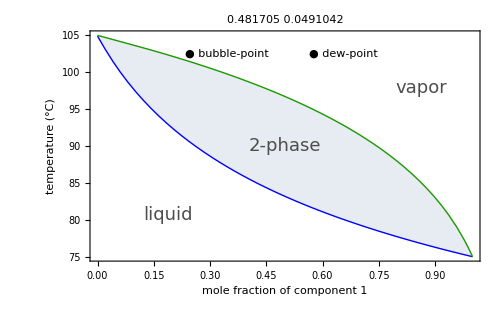

```mathematica
Module[{Pe,Psat1e,Psat2e,i,Txtable,Tytable,Txx,Tyy},
Pe=0.7;
Psat1e[Te_]=10^(9.2806-2789.51/(Te+220.64));
Psat2e[Te_]=10^(9.3935-3096.52/(Te+219.33));
i=0;
While[i<101,{xe=0.01*i,
s=FindRoot[xe*Psat1e[Te]+(1-xe)*Psat2e[Te]==Pe,{Te,90,150}];
xeq[i]=xe,
yeq[i]=(Psat1e[Te]*xe)/Pe/.s,
Teq[i]=Te/.s,i++}];
Txtable=Table[{xeq[i],Teq[i]},{i,1,100}];
Tytable=Table[{yeq[i],Teq[i]},{i,1,100}];
Txx=Interpolation[Txtable,InterpolationOrder->1];
Tyy=Interpolation[Tytable,InterpolationOrder->1];

Quiet@Plot[{Txx[x],Tyy[x]},{x,0,1},PlotLabel->Column[{Psat1e[70],Psat2e[70]}],
ImageSize->500,Frame->True,FrameLabel->{Style["mole fraction of component 1",17],Style["temperature (°C)",17]},
LabelStyle->{FontFamily->"Arial",Black},PlotStyle->{{Thick,Blue},{Thick,RGBColor[0.1,0.6,0]}},
Filling->{1->{{2},Opacity[0.1,Blend[{Blue,RGBColor[0.1,0.6,0]},0.5]]}},
Epilog->{
Inset[Row[{Style["●",20,Blue],Style[" bubble-point",16,FontFamily->"Arial"]}],Scaled[{0.35,0.9}]],
Inset[Row[{Style["●",20,RGBColor[0.1,0.6,0]],Style[" dew-point",16,FontFamily->"Arial"]}],Scaled[{0.65,0.9}]],
Inset[Style["liquid",18,Darker[Gray,0.4],FontFamily->"Arial"],Scaled[{0.2,0.2}]],
Inset[Style["vapor",18,Darker[Gray,0.4],FontFamily->"Arial"],Scaled[{0.85,0.75}]],
Inset[Style["2-phase",18,Darker[Gray,0.4],FontFamily->"Arial"],{0.5,0.5*(Txx[0.5]+Tyy[0.5])}]
}]]
```

## Mapping a T-x-y Diagram

Looking at the T-x-y diagram in Figure 12, the system is at constant pressure. As temperature is increased past the dew-point, the mixture vaporizes. Likewise if temperature is lowered below the bubble-point, the mixture will condense. The shaded region represents the 2-phase region.

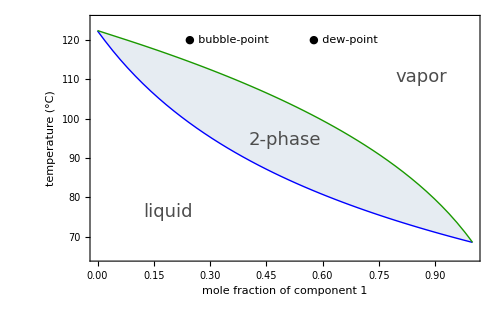
-Graphics-
Figure 12

```mathematica
Framed@Column[{Framed@Module[{Pe,Psat1e,Psat2e,i,Txtable,Tytable,Txx,Tyy},
Pe=0.7;
Psat1e[Te_]=0.00133322368*10^(6.90565-1211.033/(Te+220.79)); 
Psat2e[Te_]=0.00133322368*10^(6.65464-1344.8/(Te+219.48));  
i=0;
While[i<101,{xe=0.01*i,
s=FindRoot[xe*Psat1e[Te]+(1-xe)*Psat2e[Te]==Pe,{Te,40,190}];
xeq[i]=xe,
yeq[i]=(Psat1e[Te]*xe)/Pe/.s,
Teq[i]=Te/.s,i++}];
Txtable=Table[{xeq[i],Teq[i]},{i,1,100}];
Tytable=Table[{yeq[i],Teq[i]},{i,1,100}];
Txx=Interpolation[Txtable,InterpolationOrder->1];
Tyy=Interpolation[Tytable,InterpolationOrder->1];

Quiet@Plot[{Txx[x],Tyy[x]},{x,0,1},
PlotRange->{{0,1},{65,125}},ImageSize->500,Frame->True,FrameLabel->{Style["mole fraction of component 1",17],Style["temperature (°C)",17]},
LabelStyle->{FontFamily->"Arial",Black},PlotStyle->{{Thick,Blue},{Thick,RGBColor[0.1,0.6,0]}},
Filling->{1->{{2},Opacity[0.1,Blend[{Blue,RGBColor[0.1,0.6,0]},0.5]]}},
Epilog->{
Inset[Row[{Style["●",20,Blue],Style[" bubble-point",16,FontFamily->"Arial"]}],Scaled[{0.35,0.9}]],
Inset[Row[{Style["●",20,RGBColor[0.1,0.6,0]],Style[" dew-point",16,FontFamily->"Arial"]}],Scaled[{0.65,0.9}]],
Inset[Style["liquid",18,Darker[Gray,0.4],FontFamily->"Arial"],Scaled[{0.2,0.2}]],
Inset[Style["vapor",18,Darker[Gray,0.4],FontFamily->"Arial"],Scaled[{0.85,0.75}]],
Inset[Style["2-phase",18,Darker[Gray,0.4],FontFamily->"Arial"],{0.5,0.5*(Txx[0.5]+Tyy[0.5])}]
}]],Text@Style["Figure 12",16,Bold,FontFamily->"Arial",Darker[Cyan,0.65]]},Alignment->Center]
```

```mathematica
Manipulate[
Module[{Pe,Psat1e,Psat2e,i,Txtable,Tytable,Txx,Tyy},
Pe=0.7;
Psat1e[Te_]=0.00133322368*10^(6.90565-1211.033/(Te+220.79)); 
Psat2e[Te_]=0.00133322368*10^(6.65464-1344.8/(Te+219.48));  
i=0;
While[i<101,{xe=0.01*i,
s=FindRoot[xe*Psat1e[Te]+(1-xe)*Psat2e[Te]==Pe,{Te,40,190}];
xeq[i]=xe,
yeq[i]=(Psat1e[Te]*xe)/Pe/.s,
Teq[i]=Te/.s,i++}];
Txtable=Table[{xeq[i],Teq[i]},{i,1,100}];
Tytable=Table[{yeq[i],Teq[i]},{i,1,100}];
Txx=Interpolation[Txtable,InterpolationOrder->1];
Tyy=Interpolation[Tytable,InterpolationOrder->1];
(*x1=Quiet[xe1/.FindRoot[xe1*Psat1e[T]+(1-xe1)*Psat2e[T]==Pe,{xe1,0}]];*)

Quiet@Plot[{Txx[x],Tyy[x]},{x,0,1},PlotLabel->1,
PlotRange->{{0,1},{65,125}},ImageSize->500,Frame->True,FrameLabel->{Style["mole fraction of component 1",17],Style["temperature (°C)",17]},
LabelStyle->{FontFamily->"Arial",Black},PlotStyle->{{Thick,Blue},{Thick,RGBColor[0.1,0.6,0]}},
Filling->{1->{{2},Opacity[0.1,Blend[{Blue,RGBColor[0.1,0.6,0]},0.5]]}},Epilog->Inset[Graphics[{PointSize[Large],Point[{0,0}]}],{0.5,Temp}]]
],{{Temp,70,""},70,90}]
```